```mathematica
Clear[s, invs,g,x,u, d,rs, a, b, rho,rho1,rho2,rho3, rhodash, rhodash1, rhodash2,rhodash3, lgs, lgs1,lgs2, lgs3,lgs4,lgs5,lgs6]
```

```mathematica
w = {{-g,g},{g,-g}};
```

```mathematica
Eigenvectors[w] 
evec = {{1,1},{-1,1}}
```

{{-1,1},{1,1}}

{{1,1},{-1,1}}

```mathematica
s = Transpose[{Normalize[evec[[1]]],Normalize[evec[[2]]]}]
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
invs = Simplify[Assuming[{ab>0, ba>0},Inverse[s]]];
```

```mathematica
diagw = Simplify[invs.w.s]
```

{{0,0},{0,-2 g}}

```mathematica
bcu = {{1,0},{0,Exp[u]}};
```

```mathematica
rhodash[r_] = {{1, 1/r, 0, 0},{0, 0, Exp[-Sqrt[Abs[diagw[[2,2]]]/d]r]/r,Exp[Sqrt[Abs[diagw[[2,2]]]/d]r]/r}} /.√2 √(1/d)√Abs[g]->x
```

{{1,1/r,0,0},{0,0,ⅇ^(-r x)/r,ⅇ^(r x)/r}}

```mathematica
lgs1 = Join[rhodash[rs],{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},2];
lgs2 = Join[rhodash[a], -invs.bcu.s.rhodash[a], {{0,0,0,0},{0,0,0,0}},2];
lgs3 = Join[rhodash'[a],-rhodash'[a],{{0,0,0,0},{0,0,0,0}},2];
lgs4= Join[{{0,0,0,0},{0,0,0,0}},invs.bcu.s.rhodash[b],-rhodash[b],2];
lgs5 = Join[{{0,0,0,0},{0,0,0,0}},rhodash'[b],-rhodash'[b],2];
lgs6 = Join[{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0},{0,0,0,Infinity}},2];
```

```mathematica
lgs = Join[lgs1, lgs2, lgs3, lgs4,lgs5,lgs6,1];
```

```mathematica
lgs = lgs[[1;;11,1;;11]];
```

```mathematica
c =Assuming[{ab>0, ba>0,d>0,kt>0,b>a>rs>0}, LinearSolve[lgs,Transpose[{{0,0,0,0,0,0,0,0,0,0,1}}]]];
```

```mathematica
c = Assuming[b > a > rs > 0,Simplify[c]];
```

```mathematica
c = Join[c,{{0}}];
```

```mathematica
(*Simplify[lgs.c[[1;;11]]*)
```

```mathematica
rhodash1[r_] = rhodash[r].c[[1;;4]];
```

```mathematica
(*Simplify[rhodash1[rs]]*)
```

```mathematica
rhodash2[r_] = rhodash[r].c[[5;;8]];
```

```mathematica
(*Simplify[rhodash1[a] - invs.bcu.s.rhodash2[a]]
Simplify[rhodash1'[a] - rhodash2'[a]]*)
```

```mathematica
rhodash3[r_] = rhodash[r].c[[9;;12]];
```

```mathematica
(*Simplify[invs.bcu.s.rhodash2[b] - rhodash3[b]]
Simplify[rhodash2'[b] - rhodash3'[b]]
Simplify[rhodash3[Infinity]]*)
```

```mathematica
rho1[r_] = s.rhodash1[r];
rho2[r_] = s.rhodash2[r];
rho3[r_] = s.rhodash3[r];
```

```mathematica
n=Limit[Part[rho3[r],1]+ Part[rho3[r],2],{r->Infinity}]
```

{√2}

```mathematica
rhom1[r_] =(Part[rho1[r],1]+ Part[rho1[r],2])/n;
rhom2[r_] =(Part[rho2[r],1]+ Part[rho2[r],2])/n;
rhom3[r_] =(Part[rho3[r],1]+ Part[rho3[r],2])/n;
```

```mathematica
a=7;
b=15;
u=-4;
x=100;
rhom3[30]
```

{1+((1049199 ⅇ^2792-2098398 ⅇ^2796+1049199 ⅇ^2800+4503000 ⅇ^3592-9006000 ⅇ^3596+4503000 ⅇ^3600-3150599 ⅇ^4392-10495602 ⅇ^4396-3153799 ⅇ^4400-1049199 ⅇ^(200 (7+rs))+3153799 ⅇ^(200 (15+rs))-4503000 ⅇ^(100 (22+2 rs))+3153601 ⅇ^(2 (-4+100 (7+rs)))-2104402 ⅇ^(-4+200 (7+rs))-1052201 ⅇ^(2 (-4+100 (15+rs)))-2101598 ⅇ^(-4+200 (15+rs))-4503000 ⅇ^(-8+100 (22+2 rs))+9006000 ⅇ^(-4+100 (22+2 rs))) rs)/(30 (-1049199 ⅇ^2792+2098398 ⅇ^2796-1049199 ⅇ^2800-200 ⅇ^(100 (22+2 rs)) (4907-2202 rs)-200 ⅇ^(-8+100 (22+2 rs)) (4907-2202 rs)+400 ⅇ^(-4+100 (22+2 rs)) (4907-2202 rs)-3002 ⅇ^(-4+200 (7+rs)) (699-200 rs)-1402 ⅇ^(-4+200 (15+rs)) (1501-200 rs)+1501 ⅇ^(200 (7+rs)) (2099-200 rs)+701 ⅇ^(2 (-4+100 (15+rs))) (4501-200 rs)-1501 ⅇ^(2 (-4+100 (7+rs))) (701+200 rs)-701 ⅇ^(200 (15+rs)) (1499+200 rs)-200 ⅇ^3592 (4900+1502 rs-7 (1+100 rs))+400 ⅇ^3596 (4900+1502 rs-7 (1+100 rs))-200 ⅇ^3600 (4900+1502 rs-7 (1+100 rs))+ⅇ^4392 (-1+700 (4501-600 rs)+400 rs+4500 (-1+200 rs))+ⅇ^4400 (-1+15 (100-20000 rs)+400 rs+700 (4497+200 rs))+2 ⅇ^4396 (1+15 (100-20000 rs)-400 rs+700 (7501+200 rs))))}

```mathematica
fk[a_,b_,u_,x_]:=(-2 ⅇ^(u+2 (1+b) x) (1+a x) (-1+b x)-2 b ⅇ^((2+a+b) x) x (1+b x)+2 b ⅇ^((3 a+b) x) x (1+b x)-4 b ⅇ^(u+3 a x+b x) x (1+b x)+2 b ⅇ^(2 u+3 a x+b x) x (1+b x)+4 b ⅇ^(u+(2+a+b) x) x (1+b x)-2 b ⅇ^(2 u+(2+a+b) x) x (1+b x)+ⅇ^(4 a x) (-1+a x) (1+b x)-ⅇ^(2 (1+a) x) (-1+a x) (1+b x)-2 ⅇ^(u+4 a x) (-1+a x) (1+b x)+ⅇ^(2 u+4 a x) (-1+a x) (1+b x)-2 ⅇ^(u+2 (1+a) x) (1+a x) (1+b x)-ⅇ^(2 (u+x+b x)) (1+a x) (1+b x)-ⅇ^(2 (u+(a+b) x)) (-1+3 a x) (1+b x)+ⅇ^(2 (u+x+a x)) (1+3 a x) (1+b x)+ⅇ^(2 (1+b) x) (1+a x) (-1+3 b x)-ⅇ^(2 (a+b) x) (1+a x) (-1+3 b x)+2 ⅇ^(u+2 (a+b) x) (-1+b x+a (x-5 b x^2)))/(2 ⅇ^(u+2 (1+b) x) (1+a x) (1+(-2+b) x)+2 ⅇ^((2+a+b) x) x (-2+a-a x+a^2 x-b x)-4 ⅇ^(u+(2+a+b) x) x (-2+a-a x+a^2 x-b x)+2 ⅇ^(2 u+(2+a+b) x) x (-2+a-a x+a^2 x-b x)+2 ⅇ^(u+2 (1+a) x) (-1+(-2+a) x) (1+b x)+ⅇ^(4 a x) (-1+a x) (1+b x)-2 ⅇ^(u+4 a x) (-1+a x) (1+b x)+ⅇ^(2 u+4 a x) (-1+a x) (1+b x)+ⅇ^(2 (u+x+a x)) (1+(2+a) x) (1+b x)-ⅇ^(2 (1+a) x) (-1+(-2+3 a) x) (1+b x)+ⅇ^(2 (1+b) x) (1+a x) (-1+(2+b) x)-ⅇ^(2 (u+x+b x)) (1+a x) (1+(-2+3 b) x)-ⅇ^(2 (u+(a+b) x)) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)-ⅇ^(2 (a+b) x) (-1+(4-3 a+b) x+(-2 b+a (2+3 b)) x^2)-2 ⅇ^(u+2 (a+b) x) (1+(-4+a+b) x+(-2 b+a (2+5 b)) x^2)+2 ⅇ^((3 a+b) x) x (2+a^2 x+b x-a (1+x))-4 ⅇ^(u+3 a x+b x) x (2+a^2 x+b x-a (1+x))+2 ⅇ^(2 u+3 a x+b x) x (2+a^2 x+b x-a (1+x)));
```

```mathematica
Clear[a,b,rs,u,x]
a = 6;
b = 11;
rs = 1;
u = 3;
x/.Last[FindMaximum[{fk[a,b,u,x],x>0},{x,1}]]
x=0.5
```

0.430785

0.5

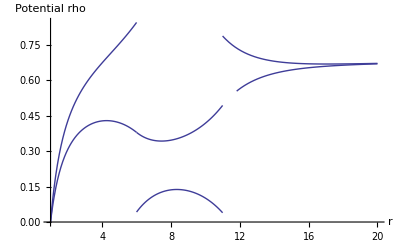

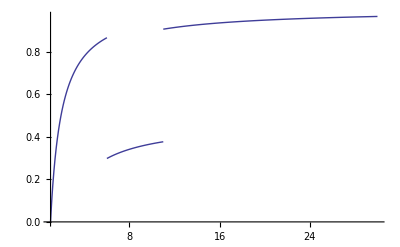

```mathematica
p3 = Plot[rho3[r], {r,b,20}];
p2 = Plot[rho2[r], {r,a,b}];
p1 = Plot[rho1[r], {r,rs,a}];
p7 = Plot[HeavisideTheta[r - a] - HeavisideTheta[r - b], {r,1,10}, Filling->Axis, AxesLabel->{r,Potential}];
p6 = Plot[rhom3[r], {r,b,30}];
p5 = Plot[rhom2[r], {r,a,b}];
p4 = Plot[rhom1[r], {r,rs,a}];
Show[p1,p2,p3, PlotRange -> All, AxesLabel->{r,Potential rho}]
Show[p4,p5,p6, PlotRange -> All]
```

```mathematica
Directory[]
```

/home/jakob

```mathematica
xvals = {0.004,0.4,4}
For [i=1,i<4,i++,
t = 5;
g=1;
a = 1+t;
b = 1+(g+1)t;
rs = 1.0;
rd = 20;
dr =0.2;
u = 3.0;
x=xvals[[i]];
filename = "table"<>ToString[i]<>".tsv";
file = OpenAppend[filename];
tab1 = Table[Flatten[{{r},rho1[r],rhom1[r]}], {r,rs,a,dr}];
tab2 = Table[Flatten[{{r},rho2[r],rhom2[r]}], {r,a,b,dr}];
tab3 = Table[Flatten[{{r},rho3[r],rhom3[r]}], {r,b,rd,dr}];
tab1[[All,2]] = tab1[[All,2]]/Last[tab3][[2]];
tab1[[All,3]] = tab1[[All,3]]/Last[tab3][[3]];
tab1[[All,4]] = tab1[[All,4]]/Last[tab3][[4]];
tab2[[All,2]] = tab2[[All,2]]/Last[tab3][[2]];
tab2[[All,3]] = tab2[[All,3]]/Last[tab3][[3]];
tab2[[All,4]] = tab2[[All,4]]/Last[tab3][[4]];
tab3[[All,2]] = tab3[[All,2]]/Last[tab3][[2]];
tab3[[All,3]] = tab3[[All,3]]/Last[tab3][[3]];
tab3[[All,4]] = tab3[[All,4]]/Last[tab3][[4]];
Last[tab3][[2]];
Export[file,tab1,"TSV"];
Export[file, "\n", "TSV"];
Export[file,tab2,"TSV"];
Export[file, "\n", "TSV"];
Export[file,tab3,"TSV"];
Export[file, "\n", "TSV"];
Close[filename];
]
```

{0.004,0.4,4}

```mathematica
Simplify[rhodash1[rs]]
N[rhodash1[a]-invs.bcu.s.rhodash2[a]]
N[invs.bcu.s.rhodash2[b]-rhodash3[b]]
N[rhodash1'[a]-rhodash2'[a]]
N[rhodash2'[b]-rhodash3'[b]]
Simplify[rhodash3[Infinity]]
```

{{0.},{0.}}

{{-1.11022×10^-16},{-2.22045×10^-16}}

{{-4.44089×10^-16},{-4.44089×10^-16}}

{{0.},{-3.33067×10^-16}}

{{0.},{2.22045×10^-16}}

{{1.},{0.}}